```mathematica
(*Line charrge Distribution and its potential*)
(*Potential Function*)
Pot[Q_,x0_,y0_,z0_]:=Q/(4Pi epsilon Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2]);
(*Define list of charges uniform distribution*)
LineCharges=Table[{0.2,x},{x,-5,5}]
```

{{0.2,-5},{0.2,-4},{0.2,-3},{0.2,-2},{0.2,-1},{0.2,0},{0.2,1},{0.2,2},{0.2,3},{0.2,4},{0.2,5}}

```mathematica
(*Compute line potential*)
```

```mathematica
LinePot=0;
Do[LinePot=LinePot+Pot[
LineCharges[[i,1]]
,LineCharges[[i,2]],0,0],{i,1,11}]
LinePot
```

0.0159155/(epsilon √((-5+x)^2+y^2+z^2))+0.0159155/(epsilon √((-4+x)^2+y^2+z^2))+0.0159155/(epsilon √((-3+x)^2+y^2+z^2))+0.0159155/(epsilon √((-2+x)^2+y^2+z^2))+0.0159155/(epsilon √((-1+x)^2+y^2+z^2))+0.0159155/(epsilon √(x^2+y^2+z^2))+0.0159155/(epsilon √((1+x)^2+y^2+z^2))+0.0159155/(epsilon √((2+x)^2+y^2+z^2))+0.0159155/(epsilon √((3+x)^2+y^2+z^2))+0.0159155/(epsilon √((4+x)^2+y^2+z^2))+0.0159155/(epsilon √((5+x)^2+y^2+z^2))

```mathematica
LinePot=LinePot/.{epsilon->1,z->0}
```

0.0159155/(√((-5+x)^2+y^2))+0.0159155/(√((-4+x)^2+y^2))+0.0159155/(√((-3+x)^2+y^2))+0.0159155/(√((-2+x)^2+y^2))+0.0159155/(√((-1+x)^2+y^2))+0.0159155/(√(x^2+y^2))+0.0159155/(√((1+x)^2+y^2))+0.0159155/(√((2+x)^2+y^2))+0.0159155/(√((3+x)^2+y^2))+0.0159155/(√((4+x)^2+y^2))+0.0159155/(√((5+x)^2+y^2))

```mathematica
(*Plot3D in xy-plane*)
Plot3D[LinePot,{x,-6,6},{y,-6,6},PlotRange->{{-6,6},{-6,6},{0,0.5}},PlotPoints->100,Boxed->False]
```

-Graphics3D-

```mathematica
Needs["VectorAnalysis`"]
```

General::obspkg: "VectorAnalysis`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Cartesian::shdw: Symbol "Cartesian" appears in multiple contexts {"VectorAnalysis`", "Global`"}; definitions in context "VectorAnalysis`" may shadow or be shadowed by other definitions.

```mathematica
(*Electric Intensity*)
LineInt=-Grad[LinePot,Cartesian[x,y,z]]
```

{(0.0159155 (-5+x))/(((-5+x)^2+y^2)^(3/2))+(0.0159155 (-4+x))/(((-4+x)^2+y^2)^(3/2))+(0.0159155 (-3+x))/(((-3+x)^2+y^2)^(3/2))+(0.0159155 (-2+x))/(((-2+x)^2+y^2)^(3/2))+(0.0159155 (-1+x))/(((-1+x)^2+y^2)^(3/2))+(0.0159155 x)/((x^2+y^2)^(3/2))+(0.0159155 (1+x))/(((1+x)^2+y^2)^(3/2))+(0.0159155 (2+x))/(((2+x)^2+y^2)^(3/2))+(0.0159155 (3+x))/(((3+x)^2+y^2)^(3/2))+(0.0159155 (4+x))/(((4+x)^2+y^2)^(3/2))+(0.0159155 (5+x))/(((5+x)^2+y^2)^(3/2)),(0.0159155 y)/(((-5+x)^2+y^2)^(3/2))+(0.0159155 y)/(((-4+x)^2+y^2)^(3/2))+(0.0159155 y)/(((-3+x)^2+y^2)^(3/2))+(0.0159155 y)/(((-2+x)^2+y^2)^(3/2))+(0.0159155 y)/(((-1+x)^2+y^2)^(3/2))+(0.0159155 y)/((x^2+y^2)^(3/2))+(0.0159155 y)/(((1+x)^2+y^2)^(3/2))+(0.0159155 y)/(((2+x)^2+y^2)^(3/2))+(0.0159155 y)/(((3+x)^2+y^2)^(3/2))+(0.0159155 y)/(((4+x)^2+y^2)^(3/2))+(0.0159155 y)/(((5+x)^2+y^2)^(3/2)),0}

```mathematica
Needs["VectorFieldPlots`"];
```

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

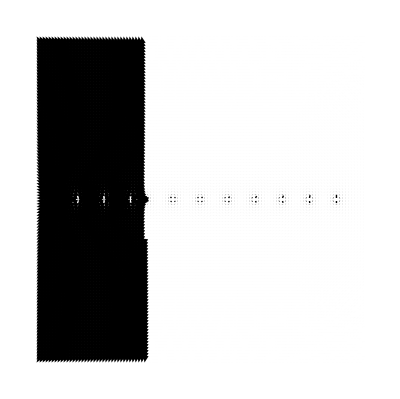

```mathematica
VectorFieldPlot[{LineInt[[1]],LineInt[[2]]},{x,-6,6,0.11},{y,-6,6,0.11}]
```

{{0.2,-5},{0.2,-4},{0.2,-3},{0.2,-2},{0.2,-1},{0.2,0},{0.2,1},{0.2,2},{0.2,3},{0.2,4},{0.2,5}}

0.0159155/(√(y^2))+0.031831/(√(1+y^2))+0.031831/(√(4+y^2))+0.031831/(√(9+y^2))+0.031831/(√(16+y^2))+0.031831/(√(25+y^2))

-Graphics3D-

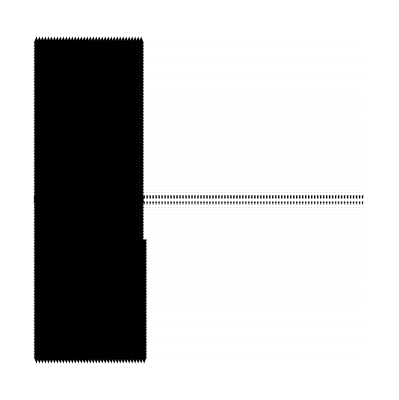

```mathematica
(*Problem:Compute and Plot Potential on two Lines parallel to x-axis and y-axis and having y-intecepts:+1,-1*)
(*Problem:Compute and plot potential on y-axis*)
(*Line charrge Distribution and its potential*)
(*Potential Function*)
x=.;y=.;
Pot[Q_,x0_,y0_,z0_]:=Q/(4Pi epsilon Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2]);
(*Define list of charges uniform distribution*)
LineCharges=Table[{0.2,y},{y,-5,5}]
(*Compute line potential*)
LinePot=0;
Do[LinePot=LinePot+Pot[
LineCharges[[i,1]]
,LineCharges[[i,2]],0,0],{i,1,11}];
LinePot=LinePot/.{epsilon->1,z->0,x->0}
(*Plot3D in xy-plane*)
Plot3D[LinePot,{x,-6,6},{y,-6,6},PlotRange->{{-6,6},{-6,6},{0,0.5}},PlotPoints->100]

(*Electric Intensity*)
LineInt=-Grad[LinePot,Cartesian[x,y,z]];

VectorFieldPlot[{LineInt[[1]],LineInt[[2]]},{x,-6,6,0.11},{y,-6,6,0.11}]
```